```mathematica
x=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
y=Range[11,20]
```

{11,12,13,14,15,16,17,18,19,20}

```mathematica
z=Table[0,10]
```

{0,0,0,0,0,0,0,0,0,0}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
li=Transpose[{x,y,z}]
```

{{1,11,0},{2,12,0},{3,13,0},{4,14,0},{5,15,0},{6,16,0},{7,17,0},{8,18,0},{9,19,0},{10,20,0}}

```mathematica
Graphics3D[Table[Cuboid[q,q+1],{q,li}]]
```

-Graphics3D-

```mathematica
Manipulate[,{}]
```

"install METEORA code for desktop"

```mathematica
trainingset={1->1.3,2->2.4,3->6.4,4->10.1}
```

{1→1.3,2→2.4,3→6.4,4→10.1}

```mathematica
p=Predict[trainingset,Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
dist=p[1.5,"Distribution"]
```

NormalDistribution[2.03329,1.04895]

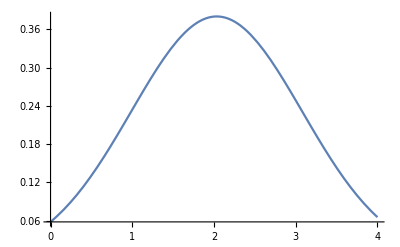

```mathematica
Plot[PDF[dist,x],{x,0,4}]
```

```mathematica
bhdata=ExampleData[{"MachineLearning","BostonHomes"},"TrainingData"];
```

```mathematica
Length@bhdata
```

338

```mathematica
RandomSample[bhdata,1]
```

{{1.13081,0,8.14,0,0.538,5.713,94.1,4.233,4,307,21,360.17,22.6}→12.7}

```mathematica
p=Predict@bhdata
```

PredictorFunction[…]

```mathematica
pm=PredictorMeasurements[p,ExampleData[{"MachineLearning","BostonHomes"},"TestData"]]
```

PredictorMeasurementsObject[…]

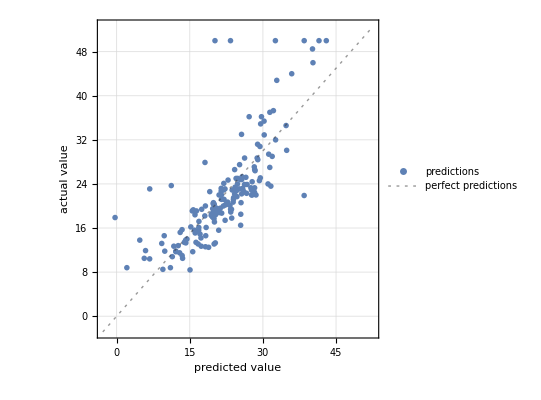

```mathematica
pm["ComparisonPlot"]
```

```mathematica
p[pm["WorstPredictedExamples"][[1,1]]]
```

20.166

```mathematica
pm["WorstPredictedExamples"]
```

{{4.89822,0,18.1,0,0.631,4.97,100,1.3325,24,666,20.2,375.52,3.26}→50,{8.26725,0,18.1,1,0.668,5.875,89.6,1.1296,24,666,20.2,347.88,8.88}→50,{18.811,0,18.1,0,0.597,4.628,100,1.5539,24,666,20.2,28.79,34.37}→17.9,{6.53876,0,18.1,1,0.631,7.016,97.5,1.2024,24,666,20.2,392.05,2.96}→50,{3.47428,0,18.1,1,0.718,8.78,82.9,1.9047,24,666,20.2,354.55,5.29}→21.9,{13.5222,0,18.1,0,0.631,3.863,100,1.5106,24,666,20.2,131.42,13.33}→23.1,{0.28955,0,10.59,0,0.489,5.412,9.8,3.5875,4,277,18.6,348.93,29.55}→23.7,{2.01019,0,19.58,0,0.605,7.929,96.2,2.0459,5,403,14.7,369.3,3.7}→50,{0.36894,22,5.86,0,0.431,8.259,8.4,8.9067,7,330,19.1,396.9,3.54}→42.8,{11.9511,0,18.1,0,0.659,5.608,100,1.2852,24,666,20.2,332.09,12.13}→27.9}

```mathematica
pm["StandardDeviation"]
```

5.7013

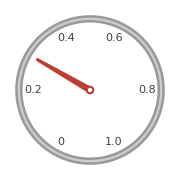

```mathematica
AngularGauge[.3]
```

```mathematica
trainingset=(Image[AngularGauge@#]->#)&/@RandomReal[1,100];
```

```mathematica
RandomSample[trainingset,2]
```

{-Graphics-→0.152263,-Graphics-→0.49519}

```mathematica
predictor=Predict@trainingset;
```

```mathematica
Row[{AngularGauge[Dynamic[t]],Style["-> ",Large],Dynamic[Labeled[AngularGauge[predictor[Image[AngularGauge[t]]]],"(predicted value)"]]}]
```

->

```mathematica
NetEncoder["Characters"]["A large cat"]
```

{36,3,79,68,85,74,72,3,70,68,87}

```mathematica
NetEncoder["Tokens"]["A large cat"]
```

{11,19234,5052}

```mathematica
c=Classify[{"the cat is grey"->-Graphics-,"my cat is fast"->-Graphics-,"this dog is scary"->-Graphics-,"the big dog"->-Graphics-},FeatureExtractor->{ToUpperCase,RemoveDiacritics,"SegmentedWords"}]
```

ClassifierFunction[…]

```mathematica
c[{"nice cat","what a dog"}]
```

{-Graphics-,-Graphics-}